```mathematica
l = {0.45, 0.2, 0.1, 0.25, 0.15}
op = {200*10^5, 700*10^5, 900 * 10^5, 500*10^5, 900*10^5}
op = {200*10^8, 700*10^8, 900 * 10^8, 500*10^8, 900*10^8}
maxV = {0.004437, 0.005376, 0.002048, 0.005461, 0.00512}
```

{0.45,0.2,0.1,0.25,0.15}

{20000000,70000000,90000000,50000000,90000000}

{20000000000,70000000000,90000000000,50000000000,90000000000}

{0.004437,0.005376,0.002048,0.005461,0.00512}

```mathematica
getQ[oper_, cpuSpeed_] := oper/cpuSpeed
getV[maxV_, l_] := maxV * l
getP[l_, q_] := l * q
getU[w_, q_] := w + Total[q]
getR[p_, k_] := Total [Table[p[[i]], {i, 1, k}]]
getW[cpu_, op_, l_, maxV_, v_] := Total[l * getQ[op, cpu]^2]*(1 + v^2)/(2(1-Total[getP[getV[maxV, l], getQ[op, cpu]]]))
getW[cpu_, op_, l_, maxV_, v_, k_] := Total[(l * getQ[op, cpu]^2) * (1 + v^2)]/(2 * (1 - getR[getP[l, getQ[op, cpu]], k]) * (1 - getR[getP[l, getQ[op, cpu]], k - 1]) )
getU[cpu_, op_, l_, maxV_, v_, k_] := getW[cpu, op, l, maxV, v, k] + getQ[op, cpu][[k]]
getP[l, getQ[op, 10^10]]
getR[getP[l, getQ[op, 10^10]], 2]
```

{0.9,1.4,0.9,1.25,1.35}

2.3

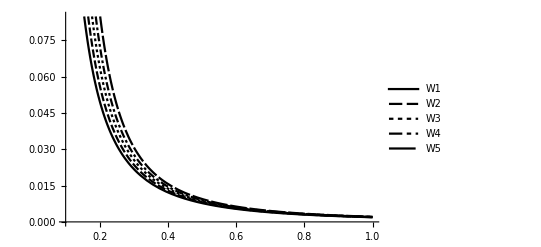

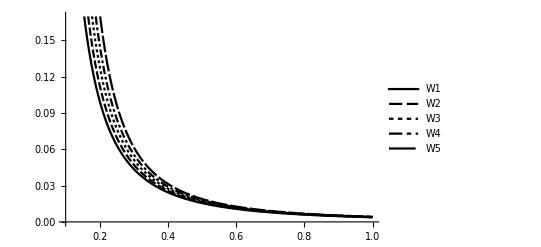

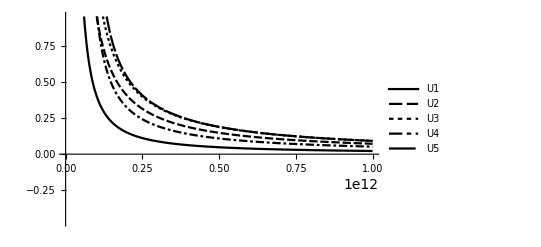

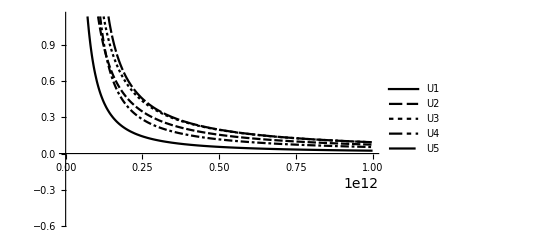

```mathematica
Plot[{getW[cpu,op,l,maxV, 0, 1], getW[cpu,op,l,maxV, 0, 2], getW[cpu,op,l,maxV, 0, 3], getW[cpu,op,l,maxV, 0, 4], getW[cpu,op,l,maxV, 0, 5]},{cpu,10^11,10^12},PlotTheme->"Monochrome", PlotLegends->{W1,W2,W3,W4,W5}]
Plot[{getW[cpu,op,l,maxV, 1, 1], getW[cpu,op,l,maxV, 1, 2], getW[cpu,op,l,maxV, 1, 3], getW[cpu,op,l,maxV, 1, 4], getW[cpu,op,l,maxV, 1, 5]},{cpu,10^11,10^12},PlotTheme->"Monochrome", PlotLegends->{W1,W2,W3,W4,W5}]
Plot[{getU[cpu,op,l,maxV, 0, 1], getU[cpu,op,l,maxV, 0, 2], getU[cpu,op,l,maxV, 0, 3], getU[cpu,op,l,maxV, 0, 4], getU[cpu,op,l,maxV, 0, 5]},{cpu,10^5,10^12},PlotTheme->"Monochrome", PlotLegends->{U1,U2,U3,U4,U5}]
Plot[{getU[cpu,op,l,maxV, 1, 1], getU[cpu,op,l,maxV, 1, 2], getU[cpu,op,l,maxV, 1, 3], getU[cpu,op,l,maxV, 1, 4], getU[cpu,op,l,maxV, 1, 5]},{cpu,10^5,10^12},PlotTheme->"Monochrome", PlotLegends->{U1,U2,U3,U4,U5}]
```

```mathematica
flist =Table[{0.5*1024/5*40,1024 / 15 * 60,0,2.5 * 1024 / 10 * 10,4 * 1024 / 20 * 10}]
o1 = Table[{1024 / 15 * 10,  4 * 1024 / 20 * 6}]
o2 = Table[{1024 / 8 * 16, 1.5  * 1024 }]
f2list = Table[{1024 / 8 * 126, 1.5*1024/6*64, 2 * 1024 / 18 * 20, 3 * 1024 / 15 * 8, 4.5 * 1024 / 25 * 13}]
o = 2*10^8 + 7 * 10^8 + 9*10^8 + 5 * 10^8 + 9 * 10^8 + Total[flist + f2list] + 1

o = Total[o1 + o2] * 2 + 200+ 1

nNorm = {{0, 1, 1, 1, 0, 0, 0, 0, 1, 0}, {1, 0, 0, 1, 0, 0, 1, 0, 1, 0}, {1, 1, 0, 1, 0, 0, 0, 0, 0, 1}, {0, 1, 1, 0, 0, 1, 0, 1, 0, 1}, {0, 1, 0, 1, 0, 0, 1, 0, 0, 1}}

vVZY1 = {0.5 * 1024, 0, 1024, 0, 1.5 * 1024, 0, 2.5 * 1024, 0, 4 * 1024, 0}
vVZY2 = {0, 1024, 0, 1.5 * 1024, 0, 2 * 1024, 0, 3 * 1024, 0, 4.5 * 1024}
gVZY1 = {5, 0, 15, 0, 14, 0, 10, 0, 20, 0}
gVZY2 = {0, 8, 0, 6, 0, 18, 0, 15, 0, 25}
qFVZY1 = {1, 0, 2, 0, 3, 0, 2.5, 0, 2.5, 0}
qFVZY2 = {0, 0.1, 0, 0.05, 0, 0.06, 0, 0.13, 0, 0.12}
```

{4096.,4096,0,2560.,2048}

{2048/3,6144/5}

{2048,1536.}

{16128,16384.,20480/9,8192/5,2396.16}

3.20005×10^9

11191.9

{{0,1,1,1,0,0,0,0,1,0},{1,0,0,1,0,0,1,0,1,0},{1,1,0,1,0,0,0,0,0,1},{0,1,1,0,0,1,0,1,0,1},{0,1,0,1,0,0,1,0,0,1}}

{512.,0,1024,0,1536.,0,2560.,0,4096,0}

{0,1024,0,1536.,0,2048,0,3072,0,4608.}

{5,0,15,0,14,0,10,0,20,0}

{0,8,0,6,0,18,0,15,0,25}

{1,0,2,0,3,0,2.5,0,2.5,0}

{0,0.1,0,0.05,0,0.06,0,0.13,0,0.12}

```mathematica
oProc = o - Total[o1 + o2]
```

2.×10^8

```mathematica
p12 = Total[o1]/o
p13 = Total[o2] / o
p10 = Total[o1 + o2] / o
p11 = 1 - p10 - p12 - p13
```

0.17079

0.320231

0.49102

0.0179594

```mathematica
a = {9, 8, 7, 6, 5, 4, 3, 2, 1, 0}
b  = Table[a[[i]], {i, 1, 3}]
Total[b]
```

{9,8,7,6,5,4,3,2,1,0}

{9,8,7}

```mathematica
Total[(vVZY2 * nNorm[[1]])/((gVZY2 * nNorm[[1]]) /. 0 -> 1)]
```

384.

```mathematica
x1 = 273
x2 = 384
n =(200 * 10^5) +(x1 + x2) + 38*(x1 + x2)
p12 = x1/n
p13 = x2 / n
p14 = 38 *(x1 + x2) / n

s3 = l[[1]] * p13
s2 = l[[1]] * p12
s4 = l[[1]] * p14
```

273

384

20025623

273/20025623

384/20025623

24966/20025623

8.62895×10^-6

6.13464×10^-6

0.000561016